```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Read the data file and reshape it *)
```

```mathematica
ncol=6;c=1;ω=0.835;m=0;
filename=StringJoin["/home/romaingrvl/MEGAsync/thèse/freefem/spinning_mini_BS/data/mathematica/dipole_data/bs_mat_om=",ToString[ω],"_m=",ToString[m],"_c=",ToString[c],".out"]
data=ReadList[filename,Number];
data=data/.$Failed->0;
nline=Length[data]/ncol;
datashaped=ArrayReshape[data,{nline,ncol}]
```

/home/romaingrvl/MEGAsync/thèse/freefem/spinning_mini_BS/data/mathematica/dipole_data/bs_mat_om=0.835_m=0_c=1.out

```mathematica
(* Check the values of the grid bounds *)
```

```mathematica
xmin=Min[datashaped[[All,1]]]
xmax=Max[datashaped[[All,1]]]
θmin=Min[datashaped[[All,2]]]
θmax=Max[datashaped[[All,2]]]
```

0

1

0

1.5708

```mathematica
(* Useful things for later *)
```

```mathematica
gridx=DeleteDuplicates[datashaped[[All,1]]];
R[x_]:=c x/(1-x);
```

```mathematica
(* Construct tabulated values of the scalar field in compactified coordinates and interpolate *)
```

```mathematica
dataϕ=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,3]]},{i,nline}];
```

```mathematica
(* ϕ: scalar field profile in compactified coordinates 
ϕρz: scalar field profile in cylindrical coordinates *)
```

```mathematica
ϕ=Interpolation[dataϕ,InterpolationOrder->3]
ϕρz[ρ_,z_]:=ϕ[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[z,ρ]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ϕ[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
ρmax=20;zmax=ρmax;
Plot3D[ϕρz[ρ,z],{ρ,0,ρmax},{z,0,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
(* Compute the coordinate distance (meaningful for dipolar stars only) *)
```

```mathematica
FindMaximum[{ϕ[x,θmin],0<=x<=1},{x,0.4}]
x0=%[[2,1,2]]
c x0/(1-x0)
%*2.0
```

{0.170441,{x→0.775952}}

0.775952

3.46333

6.92666

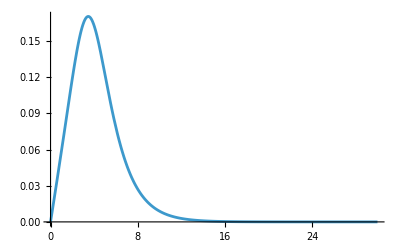

```mathematica
Plot[ϕρz[θmin,z],{z,0,1.5ρmax},PlotRange->All]
```

```mathematica
(* Construct tabulated values of ϕ-derivatives in compactified coordinates and interpolate *)
```

```mathematica
datadxϕ=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,4]]},{i,nline}];
```

```mathematica
dxϕ=Interpolation[datadxϕ,InterpolationOrder->3]
dxϕρz[ρ_,z_]:=dxϕ[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[z,ρ]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[dxϕ[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
Plot3D[dxϕρz[ρ,z],{ρ,0,ρmax},{z,0,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
(* Compute the coordinate distance (meaningful for dipolar stars only) *)
```

```mathematica
FindRoot[dxϕ[x,θmin],{x,x0}]
zcd=%[[1,2]]
c zcd/(1-zcd)
%*2
```

{x→0.775989}

0.775989

3.46406

6.92812

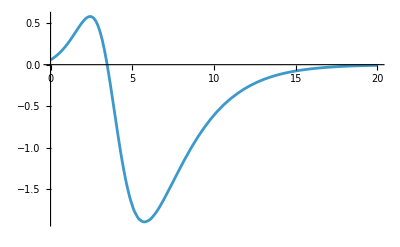

```mathematica
Plot[dxϕρz[θmin,z],{z,0,ρmax},PlotRange->All]
```

```mathematica
(* Construct tabulated values of F1 in compactified coordinates *)
```

```mathematica
dataF1=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,6]]},{i,nline}];
```

```mathematica
(* Takes only the values at θ=0 of the relevant line element for computing the distance *)
```

```mathematica
datadl=Cases[dataF1,{{x_,θmin},f_}:>{x, Exp[f]}];
dl=Interpolation[datadl,InterpolationOrder->3]
```

InterpolatingFunction[…]

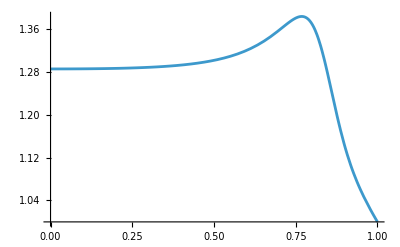

```mathematica
Plot[dl[x],{x,xmin,xmax},PlotRange->All]
```

```mathematica
(* Compute the proper distance from zcd *)
```

```mathematica
Lz=2NIntegrate[dl[x] c/(1-x)^2,{x,xmin,zcd}]
```

9.23285

```mathematica
(* Compute the balance of forces *)
```

```mathematica
outprm=Last[Import["quant.out","Table"]]
```

{0.835,137,54,1,1.03465,1.03465,1.07186,0,0,-0.581129}

```mathematica
G=1/(4π);g=1/(4π);α=0.01;(*α=Sqrt[1-ω^2];*)
M=4π*outprm[[6]];Q=4π*outprm[[7]];
```

```mathematica
Fg=(-G M^2)/(4Lz^2)
Fs=g Q^2/(4Lz^2)(1+α Lz)Exp[-α Lz]
1+Fg/Fs
```

-0.0394514

0.0421704

0.0644772

-3.36306/r^2

(3.60931 ⅇ^(-0.01 r) (1+0.01 r))/r^2

1-(0.931773 ⅇ^(0.01 r))/(1+0.01 r)

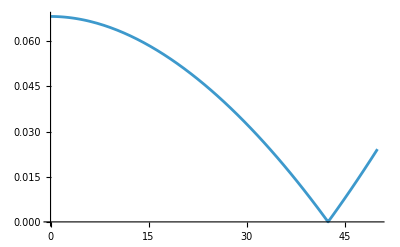

{r→42.4458}

```mathematica
Fg=(-G M^2)/(4r^2)
Fs=g Q^2/(4r^2)(1+α r)Exp[-α r]
1+Fg/Fs
Plot[Abs[%],{r,0,50}]
FindRoot[1+Fg/Fs,{r,Lz}]
```